# Chirped Detuned Raman Transfer

## Gabriel Patenotte || September 7, 2021 || Ni Group

## Notebook setup

```mathematica
Remove["Global`*"](*Clears all variables*)
padding={{70, 10}, {50, 10}}; (*Extra space surrounding a plot. Needs to be defined, else plots of the same ImageSize won't line up.*)
size=500; (*Size used for the ImageSize parameter*)
SetOptions[Plot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,ImagePadding->padding,ImageSize->size]; (*Sets Plots to have a certain look*)
SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True,FrameTicks->{Automatic,Automatic},ImagePadding->padding,ImageSize->size]; (*Sets ListPlots to have a certain look*)
```

```mathematica
messageHandler=If[Last[#],Abort[]]&

Internal`AddHandler["Message",messageHandler]
```

If[Last[#1],Abort[]]&

## Physics setup

```mathematica
μs=10^-6; (*Units*)
MHz=10^6; (*Units*)
GHz=10^9; (*Units*)
Γ=2π 10 MHz; (*Scattering from intermediate states*);
Δp=2π  21GHz; (*Detuning of the pump beam*)
ranget={0,40,.05};
ΔAC=2.59375MHz;
(*Range (in μs) and steps size (in μs) over which the ndsolve calculates the population in each state*)
```

```mathematica
width=.;
{half1,half2}=Solve[1/(√11-√10)(√11-√((t/(width/2))^2+10))==1/2,t];
width=Solve[half2⟦1,2⟧-half1⟦1,2⟧==4MHz&&width>0,width]⟦1,1,2⟧//N
```

5.69085×10^6

```mathematica
aomShape=.;
range=.;

aomShape[Δ0_,Δ1_,t_]=1/(√11-√10)(√11-√((((Δ0-ΔAC)+Δ1 t)/(width/2))^2+10));
aomShape[Δ0_,Δ1_,t_]=Clip[aomShape[Δ0,Δ1,t],{0,1}];
```

```mathematica
aomShape[2 MHz,0,t]
```

0.955443

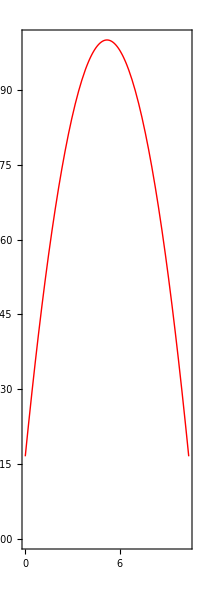

```mathematica
Plot[aomShape[0MHz,.5 MHz/μs,t μs],{t,0,2 1/(0.5 MHz)(ΔAC-0MHz)},PlotRange->{0,1},AspectRatio->3,ImageSize->200]
```

```mathematica
H[t_,Ωs_,Ωp_,Δ0_,Δ1_]=({{0, 1/2 Ωp, 1/2 √12 Ωp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2 √12 Ωp, 0, Δp+2π 3.4 GHz-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, Δ0+Δ1 t}}); (*Hamiltonian for a 4-level Λ system, with two excited intermediate states.*)
```

```mathematica
H[t,Ωs,Ωp,2.6MHz,0]//MatrixForm
```

(0 | 0.499998 Ωp | 0 | 0
0.499998 Ωp | (42000000000-10000000 ⅈ) π | 0 | Ωs/2
0 | 0 | 1.5331×10^11-3.14159×10^7 ⅈ | 0
0 | Ωs/2 | 0 | 2.6×10^6)

## Modules

```mathematica
findACShift[Ωs0_,Ωp0_]:=Module[{Ωs=Ωs0,Ωp=Ωp0},
P[t_]={p1[t],p2[t],p3[t],p4[t]};(*The population of the four states*)
init=P[0]=={1,0,0,0};(*The population is initially in the initial state*)
SE=ⅈ P'[t]==H[t,Ωs,Ωp,Δ0,0].P[t];(*The Schodinger equation*)
sols=ParametricNDSolve[{SE,init},{p1,p2,p3,p4},{t,(6.5)  μs},{Δ0},PrecisionGoal->15];
(*A parametric NDsolver, that gives a time-dependent solution as a function of Δ0*)
acData=ListPlot[Table[{Δ0,Abs[(p1[Δ0 MHz]/.sols)[(6.5)μs]]^2},{Δ0,3.5-1,3.5+1,.1}],Joined->False]]
```

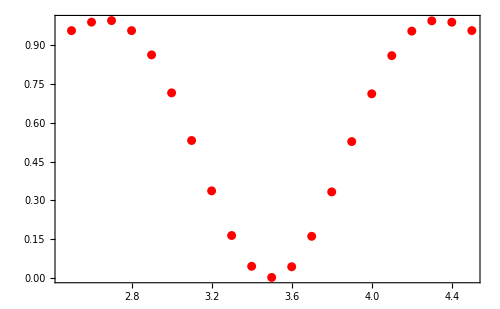

```mathematica
findACShift[2π 222 MHz,0.4 2π 37 MHz]
```

```mathematica
ﬁ
```

```mathematica
findPops[Ωs0_,Ωp0_,Δ00_,Δ10_]:=Module[{Ωs=Ωs0,Ωp=Ωp0,Δ0=Δ00,Δ1=Δ10},
P[t_]={p1[t],p2[t],p3[t],p4[t]};
(*The population in each of the four bare basis state*)
init=P[0]=={1,0,0,0};(*The population initially resides in the initial state*) 
SE=ⅈ P'[t]==H[t,Ωs,Ωp,Δ0,Δ1].P[t];(*The Schrodinger equation*)
sols=NDSolveValue[{SE,init},{p1,p2,p3,p4},{t,0,If[Δ1==0,10μs,(2(ΔAC-Δ0))/Δ1]},PrecisionGoal->8];(*We solve the Schrodinger equation. The Method is chosen to significantly reduce the evaluation time.*)
pops=Abs[#[t μs]&/@sols]^2 (*The population in each state as a function of time. The use of # here gives each of the four outputs of sols an argument of t in μs.*);{lp1,lp2,lp3,lp4}=Table[Table[{t,pops⟦i⟧},{t,0,If[Δ1==0,10,(2(ΔAC-Δ0))/Δ1],.05}],{i,1,4}](*Data for a ListPlot of the four populations over time.*)]
```

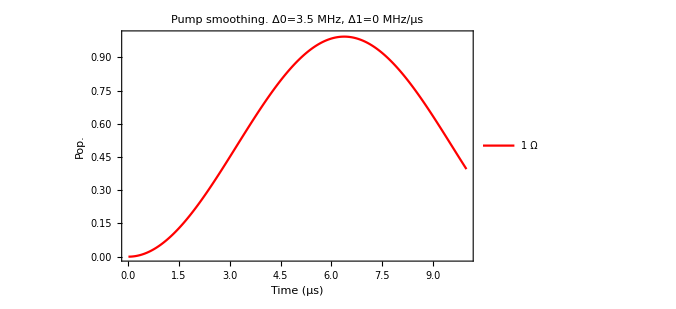

```mathematica
Δ0test=3.5;
Δ1test=0;
test1=findPops[2π 222 MHz,0.4 2π 37 MHz,Δ0test MHz,Δ1test MHz/μs];
ListPlot[{test1⟦4⟧},PlotRange->{0,1},FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["Pump smoothing. Δ0=`` MHz, Δ1=`` MHz/μs",Δ0test,Δ1test],PlotLegends->{"1 Ω","1.04 Ω","0.96 Ω"}]
```

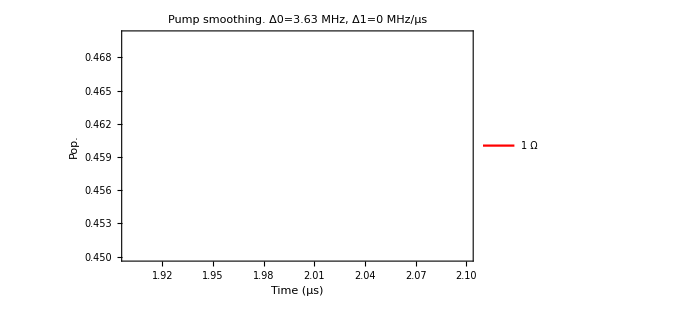

```mathematica
ListPlot[{test1⟦4⟧},PlotRange->{{1.9,2.1},{.45,.47}},FrameLabel->{"Time (μs)","Pop."},PlotLabel->StringForm["Pump smoothing. Δ0=`` MHz, Δ1=`` MHz/μs",Δ0test,Δ1test],PlotLegends->{"1 Ω","1.04 Ω","0.96 Ω"}]
```

```mathematica
π/(2.55 μs)1/MHz
```

1.232

```mathematica
NSolve[π/(((2π )222  37 x)/(2 21 1000))==6.5,x]
```

{{x→0.393325}}

```mathematica
π/%
```

2.55661

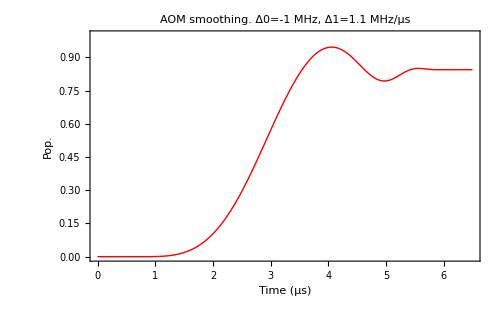

```mathematica
findPops[2π 222 MHz,2π 37 MHz,-1MHz,1.1 MHz/μs];
ListPlot[%⟦4⟧,PlotRange->{0,1},FrameLabel->{"Time (μs)","Pop."},PlotLabel->"AOM smoothing. Δ0=-1 MHz, Δ1=1.1 MHz/μs"]
```

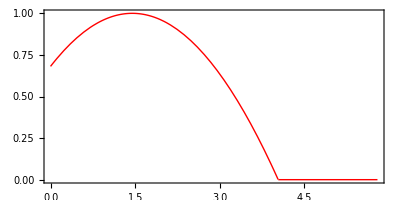

```mathematica
Plot[aomShape[1MHz,1.1 MHz/μs,t μs],{t,0,4 1/(1.1 MHz)(ΔAC-1MHz)},PlotRange->{0,1},AspectRatio->1/2,ImageSize->400]
```

```mathematica
aomShape[1MHz,1.1 MHz/μs,((ΔAC-1MHz)μs)/(1.1 MHz)+2/1.1 μs]
```

0.5

```mathematica
findACShift[Ωs0_,Ωp0_]:=Module[{Ωs=Ωs0,Ωp=Ωp0},
P[t_]={p1[t],p2[t],p3[t],p4[t]};(*The population of the four states*)
init=P[0]=={1,0,0,0};(*The population is initially in the initial state*)
SE=ⅈ P'[t]==H[t,Ωs,Ωp,Δ0,0].P[t];(*The Schodinger equation*)
sols=ParametricNDSolveValue[{SE,init},{p1,p2,p3,p4},{t,1 μs},{Δ0},PrecisionGoal->7];(*A parametric NDsolver, that gives a time-dependent solution as a function of Δ0*)
rangeΔ={0,5,1.5}; (*The population in the initial state is checked over a range of Δ0s. This defines that range.*)
n=1;
While[n<9,
popΔ=Table[Abs[sols[Δ MHz]⟦1⟧[.1μs]]^2,Evaluate@Flatten[{Δ,rangeΔ}]](*A table of the population in the initial state at 0.1μs, depending on Δ0. We choose a time that is much less than a π pulse. The Δ0 that corresponds with the lowest initial population is the 2-photon AC stark shift.*);
Δs=Table[Δ,Evaluate@Flatten[{Δ,rangeΔ}]];
minLoc=Δs⟦Ordering[popΔ,1]⟦1⟧⟧;(*The Δ0 in the current range that corresponds with the greatest population transfer. The 2-photon resonance should be a step size away from this point.*)
rangeΔ={minLoc-rangeΔ⟦3⟧,minLoc+rangeΔ⟦3⟧,2rangeΔ⟦3⟧/4};(*We specify a new range that zooms in around the minLoc.*) n++];
minLoc//N(*The while loop narrows down on a more precise range of Δ0s, such that the final minLoc is the AC stark shift up to several significant figures.*)]
```

```mathematica
findACShift[2π 222 MHz,2π 37 MHz]
```

$Aborted

```mathematica
1/(√11-√10)(√11-√(((0 (t-tpulse/2))/(width/2))^2+10))
```

1.